# Compton Analytical Calculations (2D Version)

## Constants and Prefixes

```mathematica
(*prefixes etc.*)
pC=10^-12;
μJ=10^-6;
mJ=10^-3;
nm=10^-9;
cm=10^-2;
mm=10^-3;
ps=10^-12;
fs=10^-15;
keV=10^3;
MeV=10^6;
GeV=10^9;
TeV=10^12;
mrad=10^-3;
μrad=10^-6;
μm=10^-6;
nC=10^-9;
MHz=10^6;
```

```mathematica
(*Constants*)
c=299792458;
me=0.51099895MeV;
melec=9.10938356*10^-31;
hbar=6.5821*10^-16; (*hbar in eV*)
σT=6.65245871548*10^-29;
echarge=1.60217662*10^-19;
fivedeg=(5*π)/180;
ϵ0=8.8541878128*10^-12;
μ0=1.25663706212*10^-6;
re=2.8178*10^-15; (*classical radius of the electron*)
```

## New DIANA (2D)

```mathematica
CBETA150={Ee->150MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,ϵnx->0.3mm mrad,βIPx->0.01,βIPy->0.01,ϵny->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA114={Ee->114MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,ϵnx->0.3mm mrad,βIPx->0.01,βIPy->0.01,ϵny->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA78={Ee->78MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,ϵnx->0.3mm mrad,βIPx->0.01,βIPy->0.01,ϵny->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA42={Ee->42MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,ϵnx->0.3mm mrad,βIPx->0.01,βIPy->0.01,ϵny->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
```

```mathematica
(*NEW DIANA Baseline*)
DIANA362base={Ee->362MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIPx->20cm,βIPy->20cm,ϵnx->0.5mm mrad,ϵny->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->10^-5};
DIANA717base={Ee->717MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIPx->20cm,βIPy->20cm,ϵnx->0.5mm mrad,ϵny->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->10^-5};
DIANA1072base={Ee->1072MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIPx->20cm,βIPy->20cm,ϵnx->0.5mm mrad,ϵny->0.5mm mrad,σL->25 μm,tpulse->10ps,σze->0.9mm,f->125MHz,ΔEe->10^-5,Δλ->10^-5};
```

## Optimisation + Characterisation of ICS Sources Cases

β-functions are chosen for these to correspond to transverse profile matching i.e σ_e = σ_L. Case A is a DIANA-ish ERL @ 1 GeV, Case B is the MAX-III storage ring in NEQ (upgraded rep-rate)

```mathematica
CaseA={Ee->1000MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIPx->3.53,βIPy->3.53,ϵnx->0.5mm mrad,ϵny->0.5mm mrad,σL->30μm,tpulse->10ps,σze->1mm,f->100MHz,ΔEe->10^-4,Δλ->4.66*10^-4};
CaseB={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->3nC,Epulse->100μJ,βIPx->0.066,βIPy->5.23,ϵnx->18.78mm mrad,ϵny->0.233mm mrad,σL->30μm,tpulse->10ps,σze->27.9mm,f->83.33MHz,ΔEe->6.07*10^-4,Δλ->4.66*10^-4};
CaseC={Ee->25MeV,λ->1064nm,ϕ->fivedeg,Q->10pC,Epulse->100μJ,βIPx->0.45,βIPy->0.45,ϵnx->0.1mm mrad,ϵny->0.1mm mrad,σL->30μm,tpulse->10ps,σze->0.38mm,f->100MHz,ΔEe->3*10^-4,Δλ->4.66*10^-4};
```

## FEBE ICS

```mathematica
FEBE250CASEA={Ee->250MeV,λ->800nm,ϕ->0,Q->100pC,Epulse->5,βIPx->1.23,βIPy->1.23,ϵnx->1mm mrad,ϵny->1mm mrad,σL->45 μm,tpulse->10.62fs,σze->0.72mm,f->1,ΔEe->8*10^-5,Δλ->0.03185};
FEBE250CASEB={Ee->250MeV,λ->800nm,ϕ->0,Q->100pC,Epulse->0.1,βIPx->1.23,βIPy->1.23,ϵnx->1mm mrad,ϵny->1mm mrad,σL->45 μm,tpulse->2ps,σze->0.72mm,f->1,ΔEe->8*10^-5,Δλ->0.03185};
FEBE250CASEC={Ee->250MeV,λ->1064nm,ϕ->0,Q->100pC,Epulse->60mJ,βIPx->1.23,βIPy->1.23,ϵnx->1mm mrad,ϵny->1mm mrad,σL->45 μm,tpulse->21.23ps,σze->0.72mm,f->1,ΔEe->8*10^-5,Δλ->10^-4};
```

## Intermediaries

```mathematica
(*Scattered photon energy equations*) 
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*c)/λ; (*in eV, using hbar*)
X[Ee_,ϕ_,λ_]:=(2*γ[Ee]*EL[λ]*(1+β[Ee]*Cos[ϕ]))/me;
```

```mathematica
(0.9/γ[Ee]/.CaseB)/mrad
```

0.656519

```mathematica
(*Photon production equations*)
σc[Ee_,ϕ_,λ_]:=σT*(1-X[Ee,ϕ,λ]);
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
zr[σL_,λ_]:=(4*π*σL^2)/λ;
σzl[tpulse_]:=c*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

```mathematica
(*Collimation Equations*)
ψ[Ee_,θcol_]:=γ[Ee]*θcol;
```

## a_0 Normalised Laser Vector Potential

Formula are shown for several different pulse shapes (Gaussian, Uniform Longitudinal). These formula follow Balsa Terzic’s technical note.

```mathematica
(*Gaussian*)
```

```mathematica
a0gauss[λ_,Epulse_,σL_,tpulse_]:=(echarge*Sqrt[2*c*μ0])/(2*π*melec*c^2)*λ*Sqrt[(c*Epulse)/((2*π)^(3/2)*σL^2*σzl[tpulse])];
```

```mathematica
a0gauss[λ,Epulse,σL,tpulse]/.FEBE250CASEA//ScientificForm
```

ReplaceAll::reps: {FEBE250CASEA} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2.15425×10^-6) λ √(Epulse/(tpulse σL^2))/.FEBE250CASEA

```mathematica
a0gauss[λ,Epulse,σL,tpulse]/.FEBE250CASEB//ScientificForm
```

ReplaceAll::reps: {FEBE250CASEB} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2.15425×10^-6) λ √(Epulse/(tpulse σL^2))/.FEBE250CASEB

```mathematica
a0gauss[λ,Epulse,σL,tpulse]/.FEBE250CASEC//ScientificForm
```

ReplaceAll::reps: {FEBE250CASEC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2.15425×10^-6) λ √(Epulse/(tpulse σL^2))/.FEBE250CASEC

```mathematica
(*Uniform Longitudinal - Flat top*)
```

```mathematica
a0flat[λ_,Epulse_,σL_,tpulse_]:=(echarge*Sqrt[2*c*μ0])/(2*π*melec*c^2)*λ*Sqrt[(c*Epulse)/(2*π*σL^2*σzl[tpulse])];
```

## Scattered Photon Energy

```mathematica
Eγ[Ee_,ϕ_,λ_,θ_]:=(EL[λ]*(1+β[Ee]*Cos[ϕ]))/(1-β[Ee]*Cos[θ]+EL[λ]/Ee*(1+Cos[ϕ+θ]));
```

```mathematica
Eγ[220.69MeV,0,532nm,0]/MeV
```

1.7331

```mathematica
(Eγ[Ee,ϕ,λ,0]/.FEBE250CASEC)/MeV
```

ReplaceAll::reps: {FEBE250CASEC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

((1.23984×10^-6 (1+√(1-(2.6112×10^11)/(510999.+Ee)^2) Cos[ϕ]))/(λ (1-√(1-(2.6112×10^11)/(510999.+Ee)^2)+(1.23984×10^-6 (1+Cos[ϕ]))/(Ee λ)))/.FEBE250CASEC)/1000000

## Source Size

This follows Geoff Krafft’s description which also agrees with Curatolo’s paper.

```mathematica
σxsource[βIPx_,ϵnx_,Ee_,σL_]:=(σe[βIPx,ϵnx,Ee]*σL)/Sqrt[σe[βIPx,ϵnx,Ee]^2+σL^2];
```

```mathematica
(σxsource[0.1269,0.5mm mrad,Ee,σL]/.CBETA150)/μm
```

12.6571

```mathematica
(σe[0.1269,0.5mm mrad,Ee]/.CBETA150)/μm
```

14.6771

```mathematica
σysource[βIPy_,ϵny_,Ee_,σL_]:=(σe[βIPy,ϵny,Ee]*σL)/Sqrt[σe[βIPy,ϵny,Ee]^2+σL^2];
```

```mathematica
σzsource[σze_,tpulse_]:=(σze*σzl[tpulse])/Sqrt[σze^2+σzl[tpulse]^2];
```

```mathematica
{(σxsource[βIPx,ϵnx,Ee,σL]/.FEBE250CASEC)/μm,(σysource[βIPy,ϵny,Ee,σL]/.FEBE250CASEC)/μm}//N
```

{33.4751,33.4751}

```mathematica
{(σxsource[βIPx,ϵnx,Ee,σL]/.DIANA1072base)/μm,(σysource[βIPy,ϵny,Ee,σL]/.DIANA1072base)/μm}
```

{6.65359,6.65359}

```mathematica
{(σxsource[βIPx,ϵnx,Ee,σL]/.DIANA717base)/μm,(σysource[βIPy,ϵny,Ee,σL]/.DIANA717base)/μm}
```

{7.99582,7.99582}

```mathematica
{(σxsource[βIPx,ϵnx,Ee,σL]/.DIANA362base)/μm,(σysource[βIPy,ϵny,Ee,σL]/.DIANA362base)/μm}
```

{10.7247,10.7247}

## Angular Source Size

```mathematica
σxprimesource[ϵnx_,Ee_,βIPx_,λ_]:=(Sqrt[ϵnx/(γ[Ee]*βIPx)]*Sqrt[λ/(4*π)])/Sqrt[ϵnx/(γ[Ee]*βIPx)+λ/(4*π)];
```

```mathematica
σyprimesource[ϵny_,Ee_,βIPy_,λ_]:=(Sqrt[ϵny/(γ[Ee]*βIPy)]*Sqrt[λ/(4*π)])/Sqrt[ϵny/(γ[Ee]*βIPy)+λ/(4*π)];
```

```mathematica
σxprimesource[ϵnx,Ee,βIPx,λ]/.DIANA362base//ScientificForm
```

5.81654×10^-5

```mathematica
σyprimesource[ϵny,Ee,βIPy,λ]/.DIANA362base//ScientificForm
```

5.81654×10^-5

## Head-on Luminosity

```mathematica
L[Ee_,λ_,Q_,Epulse_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_]:=(Ne[Q]*NL[Epulse,λ])/(2*π*convxy[βIPx,ϵnx,Ee,σL]*convxy[βIPy,ϵny,Ee,σL]);
```

```mathematica
L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]/.FEBE250CASEC
```

ReplaceAll::reps: {FEBE250CASEC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(5.00074×10^42 Epulse Q λ)/(√((510999. βIPx ϵnx)/(510999.+Ee)+σL^2) √((510999. βIPy ϵny)/(510999.+Ee)+σL^2))/.FEBE250CASEC

```mathematica
L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]/.DIANA362base
L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]/.DIANA717base
L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]/.DIANA1072base
```

6.94655×10^31

7.64241×10^31

7.91025×10^31

## Angular Crossing + Hourglass Effect (Miyahara)

Miayahara’s combined angular crossing and hourglass effect for geometric luminosity reduction is used here. This is based on Y. Miyahara, Luminosity of angled collision of strongly focused beams with different Gaussian distributions, NIM A, 588 (2008).

```mathematica
H[ϕ_,βIPx_,βIPy_,Ee_,ϵnx_,ϵny_,σL_,σze_,tpulse_]:=Cos[ϕ]*Sqrt[(convxy[βIPx,ϵnx,Ee,σL]^2*convxy[βIPy,ϵny,Ee,σL]^2)/(π*convz[σze,tpulse]^2)];
Ux[βIPx_,Ee_,ϵnx_,σL_,λ_]:=Sqrt[1/2*(σe[βIPx,ϵnx,Ee]^2/βIPx^2+σL^2/zr[σL,λ]^2)];
Uy[βIPy_,Ee_,ϵny_,σL_,λ_]:=Sqrt[1/2*(σe[βIPy,ϵny,Ee]^2/βIPy^2+σL^2/zr[σL,λ]^2)];
hmiy[ϕ_,βIPx_,Ee_,ϵnx_,σL_,λ_,σze_,tpulse_,Zc_]:=Sin[ϕ]^2/(convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2*Zc^2)+Cos[ϕ]^2/convz[σze,tpulse]^2;
```

```mathematica
RACHG[ϕ_,βIPx_,βIPy_,Ee_,ϵnx_,ϵny_,σL_,σze_,tpulse_,λ_]:=NIntegrate[(H[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse]*Exp[-hmiy[ϕ,βIPx,Ee,ϵnx,σL,λ,σze,tpulse,Zc]*Zc^2])/(Sqrt[convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2*Zc^2]*Sqrt[convxy[βIPy,ϵny,Ee,σL]^2+Uy[βIPy,Ee,ϵny,σL,λ]^2*Zc^2]),{Zc,-0.1,0.1},Method->"Trapezoidal"];
```

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
1/RACHG[ϕ/2,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.CBETA150
```

ReplaceAll::reps: {CBETA150} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/NIntegrate[(H[ϕ/2,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse] Exp[-hmiy[ϕ/2,βIPx,Ee,ϵnx,σL,λ,σze,tpulse,Zc] Zc^2])/(√(convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2 Zc^2) √(convxy[βIPy,ϵny,Ee,σL]^2+Uy[βIPy,Ee,ϵny,σL,λ]^2 Zc^2)),{Zc,-0.1,0.1},Method→Trapezoidal]/.CBETA150

```mathematica
RACHG[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.DIANA362base//AbsoluteTiming
```

ReplaceAll::reps: {DIANA362base} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{0.102787,NIntegrate[(H[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse] Exp[-hmiy[ϕ,βIPx,Ee,ϵnx,σL,λ,σze,tpulse,Zc] Zc^2])/(√(convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2 Zc^2) √(convxy[βIPy,ϵny,Ee,σL]^2+Uy[βIPy,Ee,ϵny,σL,λ]^2 Zc^2)),{Zc,-0.1,0.1},Method→Trapezoidal]/.DIANA362base}

```mathematica
RACHG[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.DIANA717base//AbsoluteTiming
```

{0.0092152,0.0959256}

```mathematica
RACHG[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.DIANA1072base//AbsoluteTiming
```

{0.0109275,0.0943024}

```mathematica
RAC[βIPx_,ϵnx_,Ee_,σL_,ϕ_,σze_,tpulse_]:= (convxy[βIPx,ϵnx,Ee,σL]*Cos[ϕ])/Sqrt[convxy[βIPx,ϵnx,Ee,σL]^2*Cos[ϕ]^2+convz[σze,tpulse]^2*Sin[ϕ]^2];
```

```mathematica
RAC[11.05,ϵnx,Ee,σL,ϕ,σze,tpulse]/.CaseB
```

0.156983

```mathematica
1/RAC[βIPx,ϵnx,Ee,σL,ϕ/2,σze,tpulse]/.CBETA150
```

5.56543

```mathematica
RACϕ=Table[{ϕ/mrad,RAC[βIPx,ϵnx,Ee,σL,ϕ,σze,tpulse]/.DIANA1072base},{ϕ,0.01mrad,10mrad,0.01mrad}];
```

```mathematica
RACϕplt=ListLinePlot[RACϕ,Frame->True,FrameLabel->{"Crossing Angle [mrad]","R_AC"},PlotStyle->Red,LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium];
```

```mathematica
RACϕfacplt=ListLinePlot[Partition[Riffle[RACϕ⟦All,1⟧,1/RACϕ⟦All,2⟧],2],Frame->True,FrameLabel->{"Crossing Angle [mrad]","1/R_AC Factor"},PlotStyle->Red,LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium];
```

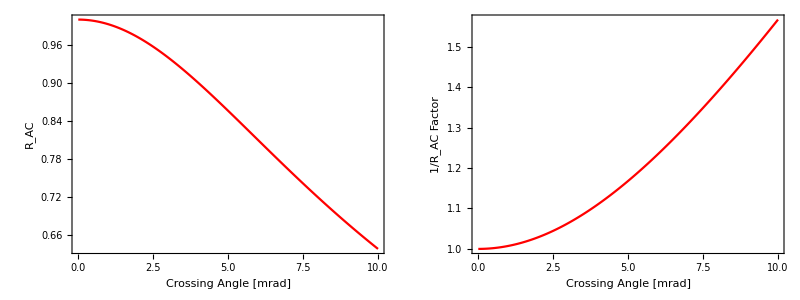

```mathematica
RACϕDIANA1072=Grid[{{RACϕplt,RACϕfacplt}}]
```

## Uncollimated Flux

```mathematica
F[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σc[Ee,ϕ,λ]*RACHG[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]*L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]*f;
```

```mathematica
F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEC//ScientificForm
```

ReplaceAll::reps: {FEBE250CASEC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(√(((5.10999×10^5) βIPx ϵnx)/(5.10999×10^5+Ee)+σL^2) √(((5.10999×10^5) βIPy ϵny)/(5.10999×10^5+Ee)+σL^2))(3.32672×10^14) Epulse f Q λ (1-((9.49631×10^-18) (5.10999×10^5+Ee) (1+√(1-(2.6112×10^11)/((5.10999×10^5+Ee)^2)) Cos[ϕ]))/λ) NIntegrate[(H[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse] Exp[-hmiy[ϕ,βIPx,Ee,ϵnx,σL,λ,σze,tpulse,Zc] Zc^2])/(√(convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2 Zc^2) √(convxy[βIPy,ϵny,Ee,σL]^2+Uy[βIPy,Ee,ϵny,σL,λ]^2 Zc^2)),{Zc,-1.×10^-1,1.×10^-1},Method→Trapezoidal]/.FEBE250CASEC

```mathematica
F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base
```

5.77181×10^10

```mathematica
F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA717base
```

6.01824×10^10

```mathematica
F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA1072base
```

6.08451×10^10

## Spectral Density (Whole Spectrum)

Spectral density is the photon density per unit energy in units of s^-1 eV^-1. Defined in many different sources

```mathematica
S[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/Eγ[Ee,ϕ,λ,0];
```

```mathematica
S[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEC
```

ReplaceAll::reps: {FEBE250CASEC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2.68319×10^20 Epulse f Q λ^2 (1-√(1-(2.6112×10^11)/(510999.+Ee)^2)+(1.23984×10^-6 (1+Cos[ϕ]))/(Ee λ)) (1-(9.49631×10^-18 (510999.+Ee) (1+√(1-(2.6112×10^11)/(510999.+Ee)^2) Cos[ϕ]))/λ) NIntegrate[(H[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse] Exp[-hmiy[ϕ,βIPx,Ee,ϵnx,σL,λ,σze,tpulse,Zc] Zc^2])/(√(convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2 Zc^2) √(convxy[βIPy,ϵny,Ee,σL]^2+Uy[βIPy,Ee,ϵny,σL,λ]^2 Zc^2)),{Zc,-0.1,0.1},Method→Trapezoidal])/(√((510999. βIPx ϵnx)/(510999.+Ee)+σL^2) √((510999. βIPy ϵny)/(510999.+Ee)+σL^2) (1+√(1-(2.6112×10^11)/(510999.+Ee)^2) Cos[ϕ]))/.FEBE250CASEC

```mathematica
S[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base
```

24811.6

```mathematica
S[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA717base
```

6645.34

```mathematica
S[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA1072base
```

3025.73

## Source Sizes + Divergences (Angular Source Size) Comparision [INVESTIGATION]

There are two different ways of calculating average brilliance in the literature. One seems to use the source size (σ_e σ_L)/Sqrt[σ_e^2+σ_L^2] and the other seems to use the source size Sqrt[σ_e^2+σ_L^2]. I am trying to compare the two to see look at a potential inconsistency in K.E. Deitrick et al, PRAB 21, 080703 (2018) and the literature more generally. It appears this originates from FEL by K. J. Kim (see handbook of acc physics). The first source size is the correct method.

```mathematica
σxsource2[βIPx_,ϵnx_,Ee_,σL_]:=Sqrt[σe[βIPx,ϵnx,Ee]^2+σL^2];
```

```mathematica
σysource2[βIPy_,ϵny_,Ee_,σL_]:=Sqrt[σe[βIPy,ϵny,Ee]^2+σL^2];
```

```mathematica
σxprimesource2[ϵnx_,Ee_,βIPx_,λ_]:=Sqrt[ϵnx/(γ[Ee]*βIPx)+λ/(4*π)];
```

```mathematica
σyprimesource2[ϵny_,Ee_,βIPy_,λ_]:=Sqrt[ϵny/(γ[Ee]*βIPy)+λ/(4*π)];
```

```mathematica
1/μm*Sqrt[1/((1/σe[βIPx,ϵnx,Ee]^2+1/σL^2)/.DIANA362base)]
```

10.7247

```mathematica
Grid[{{"DIANA ICS (Baseline) σ_γ : Source (Angular) Size Comparison",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Case"," σ_γ=σ_e/(√SuperscriptBox[SubscriptBox[σ, e], 2] + SuperscriptBox[SubscriptBox[σ, L], 2])",SpanFromLeft,SpanFromLeft,SpanFromLeft,"σ_γ=√σ_e^2+σ_L^2",SpanFromLeft,SpanFromLeft,SpanFromLeft,"Units"},
{"Parameter","σ_(γ, x)","σ_(γ, y)","σ_(γ, x')","σ_(γ, y')","σ_(γ, x)","σ_(γ, y)","σ_(γ, x')","σ_(γ, y')",""},{StringForm["DIANA `` MeV",DIANA362base⟦1,2⟧/MeV],(σxsource[βIPx,ϵnx,Ee,σL]/.DIANA362base)/μm,(σysource[βIPy,ϵny,Ee,σL]/.DIANA362base)/μm,(σxprimesource[ϵnx,Ee,βIPx,λ]/.DIANA362base)/μrad,(σyprimesource[ϵny,Ee,βIPy,λ]/.DIANA362base)/μrad,(σxsource2[βIPx,ϵnx,Ee,σL]/.DIANA362base)/μm,(σysource2[βIPy,ϵny,Ee,σL]/.DIANA362base)/μm,(σxprimesource2[ϵnx,Ee,βIPx,λ]/.DIANA362base)/μrad,(σyprimesource2[ϵny,Ee,βIPy,λ]/.DIANA362base)/μrad,"μm/μrad"},{StringForm["DIANA `` MeV",DIANA717base⟦1,2⟧/MeV],(σxsource[βIPx,ϵnx,Ee,σL]/.DIANA717base)/μm,(σysource[βIPy,ϵny,Ee,σL]/.DIANA717base)/μm,(σxprimesource[ϵnx,Ee,βIPx,λ]/.DIANA717base)/μrad,(σyprimesource[ϵny,Ee,βIPy,λ]/.DIANA717base)/μrad,(σxsource2[βIPx,ϵnx,Ee,σL]/.DIANA717base)/μm,(σysource2[βIPy,ϵny,Ee,σL]/.DIANA717base)/μm,(σxprimesource2[ϵnx,Ee,βIPx,λ]/.DIANA717base)/μrad,(σyprimesource2[ϵny,Ee,βIPy,λ]/.DIANA717base)/μrad,"μm/μrad"},{StringForm["DIANA `` MeV",DIANA1072base⟦1,2⟧/MeV],(σxsource[βIPx,ϵnx,Ee,σL]/.DIANA1072base)/μm,(σysource[βIPy,ϵny,Ee,σL]/.DIANA1072base)/μm,(σxprimesource[ϵnx,Ee,βIPx,λ]/.DIANA1072base)/μrad,(σyprimesource[ϵny,Ee,βIPy,λ]/.DIANA1072base)/μrad,(σxsource2[βIPx,ϵnx,Ee,σL]/.DIANA1072base)/μm,(σysource2[βIPy,ϵny,Ee,σL]/.DIANA1072base)/μm,(σxprimesource2[ϵnx,Ee,βIPx,λ]/.DIANA1072base)/μrad,(σyprimesource2[ϵny,Ee,βIPy,λ]/.DIANA1072base)/μrad,"μm/μrad"}},Dividers->{{True,True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True}}]
```

DIANA ICS (Baseline) σ_γ : Source (Angular) Size Comparison |  |  |  |  |  |  |  |  | 
Case |  σ_γ=σ_e/(√SuperscriptBox[SubscriptBox[σ, e], 2] + SuperscriptBox[SubscriptBox[σ, L], 2]) |  |  |  | σ_γ=√σ_e^2+σ_L^2 |  |  |  | Units
Parameter | σ_(γ, x) | σ_(γ, y) | σ_(γ, x') | σ_(γ, y') | σ_(γ, x) | σ_(γ, y) | σ_(γ, x') | σ_(γ, y') | 
DIANA 362 MeV | 10.7247 | 10.7247 | 58.1654 | 58.1654 | 27.676 | 27.676 | 296.976 | 296.976 | μm/μrad
DIANA 717 MeV | 7.99582 | 7.99582 | 41.7587 | 41.7587 | 26.3859 | 26.3859 | 294.025 | 294.025 | μm/μrad
DIANA 1072 MeV | 6.65359 | 6.65359 | 34.2725 | 34.2725 | 25.9354 | 25.9354 | 293.021 | 293.021 | μm/μrad

## Average Brilliance (Krafft) [INVESTIGATION]

The three average brilliance equations presented by K.E. Deitrick et al, PRAB 21, 080703 (2018) have been tested out here.
• Bavg1 is Eq (6), the general form, using the source sizes how I believe they should be derived. The rest, unless specified use source sizes.
• Bavg2 is Eq (6), the general form, using the source sizes how K.J. Kim + Handbook + Krafft -Comp Sources of EM Rad describe them.
• BavgNDLB is Eq (7), for non-diffraction limited laser beams, where the laser pulse divergence is negligible - just not true! I feel it is a poor approximation, laser divergence >> e^- divergence.
• BavgEB is Eq (8), where the source size is taken to be the size of the electron beam, which is okay when σ_L~σ_e but not the nicest approximation (whole point of my optimisations!)

```mathematica
F01[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=1.5*10^-3*F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f];
```

```mathematica
(*unit conversion*)
mm2mrad2=mm^2*mrad^2//N;
```

```mathematica
Bavg1[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=F01[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/(4*π^2*σxsource[βIPx,ϵnx,Ee,σL]*σxprimesource[ϵnx,Ee,βIPx,λ]*σysource[βIPy,ϵny,Ee,σL]*σxprimesource[ϵny,Ee,βIPy,λ])*mm2mrad2;
```

```mathematica
Bavg2[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=F01[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/(4*π^2*Sqrt[σe[βIPx,ϵnx,Ee]^2+σL^2]*Sqrt[σe[βIPy,ϵny,Ee]^2+σL^2]*Sqrt[(ϵnx/(γ[Ee]*βIPx))+(λ/(4*π))]*Sqrt[(ϵny/(γ[Ee]*βIPy))+(λ/(4*π))])*mm2mrad2;
```

```mathematica
BavgNDLB1[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=F01[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/(4*π^2*σxsource[βIPx,ϵnx,Ee,σL]*Sqrt[ϵnx/(γ[Ee]*βIPx)]*σysource[βIPy,ϵny,Ee,σL]*Sqrt[ϵny/(γ[Ee]*βIPy)])*mm2mrad2;
```

```mathematica
BavgNDLB2[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=F01[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/(4*π^2*σxsource2[βIPx,ϵnx,Ee,σL]*Sqrt[ϵnx/(γ[Ee]*βIPx)]*σysource2[βIPy,ϵny,Ee,σL]*Sqrt[ϵny/(γ[Ee]*βIPy)])*mm2mrad2;
```

```mathematica
BavgEB[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=(γ[Ee]^2*F01[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f])/(4*π^2*ϵnx*ϵny)*mm2mrad2;
```

```mathematica
Bavg1[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEC
```

ReplaceAll::reps: {FEBE250CASEC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(6.083×10^-13 Epulse f Q √((510999. ϵnx)/((510999.+Ee) βIPx)+λ/(4 π)) √((510999. ϵny)/((510999.+Ee) βIPy)+λ/(4 π)) (1-(9.49631×10^-18 (510999.+Ee) (1+√(1-(2.6112×10^11)/(510999.+Ee)^2) Cos[ϕ]))/λ) NIntegrate[(H[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse] Exp[-hmiy[ϕ,βIPx,Ee,ϵnx,σL,λ,σze,tpulse,Zc] Zc^2])/(√(convxy[βIPx,ϵnx,Ee,σL]^2+Ux[βIPx,Ee,ϵnx,σL,λ]^2 Zc^2) √(convxy[βIPy,ϵny,Ee,σL]^2+Uy[βIPy,Ee,ϵny,σL,λ]^2 Zc^2)),{Zc,-0.1,0.1},Method→Trapezoidal])/(√(ϵnx/((510999.+Ee) βIPx)) √((βIPx ϵnx)/(510999.+Ee)) √(ϵny/((510999.+Ee) βIPy)) √((βIPy ϵny)/(510999.+Ee)) σL^2)/.FEBE250CASEC

```mathematica
Grid[{{"DIANA ICS B_avg : Eq. from K. Deitrick et al, PRAB 21, 080703 (2018)",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},{"Source Size Calc.","σ_γ=σ_e/(√SuperscriptBox[SubscriptBox[σ, e], 2] + SuperscriptBox[SubscriptBox[σ, L], 2])",SpanFromLeft,"σ_γ=√σ_e^2+σ_L^2",SpanFromLeft,"N/A (no difference)",""},{"Case","General Form (6) ","Non-Diffraction Limited Beam (7)","General Form (6)","Non-Diffraction Limited Beam (7)","Electron Beam Approximation (8)","Units"},{StringForm["DIANA `` MeV",DIANA362base⟦1,2⟧/MeV],Bavg1[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base,BavgNDLB1[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base,Bavg2[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base,BavgNDLB2[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base,BavgEB[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base,"ph/(s mm^2-mrad^2 0.1% BW)"},{StringForm["DIANA `` MeV",DIANA717base⟦1,2⟧/MeV],Bavg1[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA717base,BavgNDLB1[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA717base,Bavg2[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA717base,BavgNDLB2[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA717base,BavgEB[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA717base,"ph/(s mm^2-mrad^2 0.1% BW)"},{StringForm["DIANA `` MeV",DIANA1072base⟦1,2⟧/MeV],Bavg1[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA1072base,BavgNDLB1[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA1072base,Bavg2[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA1072base,BavgNDLB2[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA1072base,BavgEB[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA1072base,"ph/(s mm^2-mrad^2 0.1% BW)"}},Dividers->{{True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True}}]
```

DIANA ICS B_avg : Eq. from K. Deitrick et al, PRAB 21, 080703 (2018) |  |  |  |  |  | 
Source Size Calc. | σ_γ=σ_e/(√SuperscriptBox[SubscriptBox[σ, e], 2] + SuperscriptBox[SubscriptBox[σ, L], 2]) |  | σ_γ=√σ_e^2+σ_L^2 |  | N/A (no difference) | 
Case | General Form (6)  | Non-Diffraction Limited Beam (7) | General Form (6) | Non-Diffraction Limited Beam (7) | Electron Beam Approximation (8) | Units
DIANA 362 MeV | 5.63563×10^12 | 5.41044×10^12 | 3.24635×10^10 | 8.12453×10^11 | 4.41475×10^12 | ph/(s mm^2-mrad^2 0.1% BW)
DIANA 717 MeV | 2.05107×10^13 | 2.00883×10^13 | 3.79915×10^10 | 1.84469×10^12 | 1.80334×10^13 | ph/(s mm^2-mrad^2 0.1% BW)
DIANA 1072 MeV | 4.44584×10^13 | 4.38416×10^13 | 4.00288×10^10 | 2.88545×10^12 | 4.07362×10^13 | ph/(s mm^2-mrad^2 0.1% BW)

## Peak Brilliance - My Version

Essentially this is a source size averaged version of the average brilliance.

```mathematica
N01[Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_]:=σc[Ee,ϕ,λ]*RACHG[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]*L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL];
```

```mathematica
Bpk[σze_,tpulse_,Ee_,ϕ_,λ_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,Q_,Epulse_]:=c/(2*Sqrt[2*Log[2]]*σzsource[σze,tpulse])*N01[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse]/(4*π^2*σxsource[βIPx,ϵnx,Ee,σL]*σxprimesource[ϵnx,Ee,βIPx,λ]*σysource[βIPy,ϵny,Ee,σL]*σxprimesource[ϵny,Ee,βIPy,λ])*mm2mrad2;
```

```mathematica
Bpk[σze,tpulse,Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,Q,Epulse]/.CBETA42
```

1.43344×10^17

```mathematica
Bpk[σze,tpulse,Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,Q,Epulse]/.CBETA78
```

3.03332×10^17

```mathematica
Bpk[σze,tpulse,Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,Q,Epulse]/.CBETA114
```

5.01075×10^17

```mathematica
Bpk[σze,tpulse,Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,Q,Epulse]/.CBETA150
```

7.36507×10^17

## Peak Brilliance 1D (Hartemann, Head-on, Thomson Regime, Round Beam)

Follows Hartemann and Brown, High-energy scaling of Compton scattering light sources, 8, 100702 (2005). See my thesis discussion for which peak brilliance is best when.
• Only works is the low electron recoil i.e Thomson Regime.
• Only works for a head-on interaction (ϕ=0).
• Only works for round transverse electron bunches at the IP.
• Poorly accounts for luminosity reduction - overlap factor attempts to take into account the Furman analytical hourglass effect.

```mathematica
Δuperp[βIPx_,ϵnx_,Ee_]:=ϵnx/σe[βIPx,ϵnx,Ee];
ω0[λ_]:=(2*π*c)/λ;
ωx[Ee_,λ_]:=4*γ[Ee]^2*ω0[λ];
δω[λ_,tpulse_]:=Sqrt[2]/(ω0[λ]*tpulse);
δγ[ΔEe_]:=2*ΔEe;
kf[βIPx_,ϵnx_,Ee_]:=ϵnx/(γ[Ee]*σe[βIPx,ϵnx,Ee]^2);
zr[σL_,λ_]:=(π*σL^2)/λ;
χ[λ_,Ee_]:=ωx[Ee,λ]/(4*γ[Ee]^2*ω0[λ]);
```

```mathematica
(*Intermediaries*)
```

```mathematica
η[βIPx_,ϵnx_,Ee_,tpulse_]:=(kf[βIPx,ϵnx,Ee]*c*tpulse)/(2*Sqrt[2]);
μ[σL_,λ_,tpulse_]:=(c*tpulse)/(2*Sqrt[2]*zr[σL,λ]);
```

```mathematica
(*Overlap Parameter*)
```

```mathematica
overlap[βIPx_,ϵnx_,Ee_,tpulse_,σL_,λ_]:=(η[βIPx,ϵnx,Ee,tpulse]*Exp[1/η[βIPx,ϵnx,Ee,tpulse]^2]*(Erf[1/η[βIPx,ϵnx,Ee,tpulse]]-1)-μ[σL,λ,tpulse]*Exp[1/μ[σL,λ,tpulse]^2]*(Erf[1/μ[σL,λ,tpulse]]-1))/(μ[σL,λ,tpulse]^2-η[βIPx,ϵnx,Ee,tpulse]^2);
```

why is the overlap zero for the PERLE case??

```mathematica
(*Individual Terms*)
```

```mathematica
term1[λ_,Ee_,ϵnx_,βIPx_,tpulse_,ΔEe_]:=(χ[λ,Ee]-1)/(χ[λ,Ee]*Δuperp[βIPx,ϵnx,Ee]^2)+(δω[λ,tpulse]^2+δγ[ΔEe]^2*χ[λ,Ee]^2)/(4*χ[λ,Ee]^2*Δuperp[βIPx,ϵnx,Ee]^4);
term2[λ_,Ee_,ϵnx_,βIPx_,tpulse_,ΔEe_]:=(χ[λ,Ee]-1)/Sqrt[δω[λ,tpulse]^2+δγ[ΔEe]^2*χ[λ,Ee]^2]+Sqrt[δω[λ,tpulse]^2+δγ[ΔEe]^2*χ[λ,Ee]^2]/(2*χ[λ,Ee]*Δuperp[βIPx,ϵnx,Ee]^2);
```

```mathematica
(*Peak Brilliance calculation*)
```

```mathematica
Bpeak[Ee_,ϵnx_,Q_,Epulse_,λ_,σze_,σL_,βIPx_,tpulse_,ΔEe_]:=(4*10^-15)/π^2*γ[Ee]^2/ϵnx^2*(Ne[Q]*NL[Epulse,λ])/(σze/c)*re^2/σL^2*Exp[term1[λ,Ee,ϵnx,βIPx,tpulse,ΔEe]]*(1-Erf[term2[λ,Ee,ϵnx,βIPx,tpulse,ΔEe]])*overlap[βIPx,ϵnx,Ee,tpulse,σL,λ];
```

```mathematica
Bpeak[Ee,ϵnx,Q,Epulse,λ,σze,σL,βIPx,tpulse,ΔEe]/.DIANA362base
Bpeak[Ee,ϵnx,Q,Epulse,λ,σze,σL,βIPx,tpulse,ΔEe]/.DIANA717base
Bpeak[Ee,ϵnx,Q,Epulse,λ,σze,σL,βIPx,tpulse,ΔEe]/.DIANA1072base
```

5.60332×10^17

2.22344×10^18

4.98957×10^18

## Bandwidth

Follows the Ranjan bandwidth in N. Ranjan et al, Simulation of inverse Compton scattering and its implications on the scattered linewidth, PRAB 21, 030701 (2018). This is favoured as it is for the non-round situation and takes into account all the effects that matter most to linear ICS sources. A full discussion of others can be found in my thesis.

```mathematica
collterm[Ee_,λ_,θcol_,ϕ_]:=1/Sqrt[12]*ψ[Ee,θcol]^2/(1+X[Ee,ϕ,λ]+ψ[Ee,θcol]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θcol_,ϕ_]:=(2+X[Ee,ϕ,λ])/(1+X[Ee,ϕ,λ]+ψ[Ee,θcol]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θcol_,ϕ_]:=(1+ψ[Ee,θcol]^2)/(1+X[Ee,ϕ,λ]+ψ[Ee,θcol]^2)*Δλ;
emittanceterm[Ee_,ϵnx_,ϵny_,ϕ_,λ_,βIPx_,βIPy_]:=(Sqrt[2]*γ[Ee])/(1+X[Ee,ϕ,λ])*Sqrt[ϵnx^2/βIPx^2+ϵny^2/βIPy^2];
```

```mathematica
rmsBandwidth[Ee_,λ_,θcol_,ϕ_,ΔEe_,Δλ_,ϵnx_,ϵny_,βIPx_,βIPy_]:=Sqrt[collterm[Ee,λ,θcol,ϕ]^2+beamspreadterm[Ee,λ,ΔEe,θcol,ϕ]^2+laserspreadterm[Ee,λ,Δλ,θcol,ϕ]^2+emittanceterm[Ee,ϵnx,ϵny,ϕ,λ,βIPx,βIPy]^2];
```

```mathematica
100*rmsBandwidth[Ee,λ,(0.1/γ[Ee]/.CaseB)/mrad mrad,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.CaseB
```

54.4856

```mathematica
Fcol[Ee,ϕ,λ,2.6332mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.CaseC
```

8.35206×10^7

## Minimum Theoretical Bandwidth

Limit of the bandwidth once the collimation angle has been minimised and the β^*-function at the IP has been maximised. The minimum theoretical bandwidth is a term that relates to the minimum achievable bandwidth of a particular ICS source design based on its energy spreads. It is the low energy limit observed in the tuning curve optimisations.

```mathematica
MTB[Ee_,ϕ_,λ_,ΔEe_,Δλ_]:=Sqrt[((2+X[Ee,ϕ,λ])/(1+X[Ee,ϕ,λ])*ΔEe)^2+(1/(1+X[Ee,ϕ,λ])*Δλ)^2];
```

```mathematica
MTB[Ee,ϕ,λ,ΔEe,Δλ]/.CBETA150//ScientificForm
```

1.19443×10^-3

```mathematica
100*MTB[Ee,ϕ,λ,ΔEe,Δλ]/.DIANA362base
```

0.00222746

```mathematica
100*MTB[Ee,ϕ,λ,ΔEe,Δλ]/.DIANA717base
```

0.00221914

```mathematica
MTB[Ee,ϕ,λ,ΔEe,Δλ]/.DIANA1072base//ScientificForm
```

2.21093×10^-5

## Collimated Flux

Follows my derivation of the collimated flux into an angle θ. Proves that Curatolo et al, Analytical description of photon beam phase spaces in inverse Compton scattering sources, PRAB 20, 080701 (2017) is wrong. Has veen benchmarked against yields from ICARUS and ICCS3D with surprisingly high accuracy.

### Y Lorentz Invariant

```mathematica
Y[Ee_,ϕ_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,ϕ,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

```mathematica
dσdY[Ee_,ϕ_,λ_,θ_]:=(8*π*re^2)/X[Ee,ϕ,λ]^2*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

### Collimated Cross Section

```mathematica
dYdθ[Ee_,θ_,ϕ_,λ_]:=(X[Ee,ϕ,λ]*β[Ee]*Sin[θ]*(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)-X[Ee,ϕ,λ]*(1-β[Ee]*Cos[θ])*(β[Ee]*Sin[θ]-EL[λ]/Ee*Sin[ϕ+θ]))/(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)^2
```

```mathematica
dσdθ[Ee_,ϕ_,λ_,θ_]:=dσdY[Ee,ϕ,λ,θ]*dYdθ[Ee,θ,ϕ,λ];
```

```mathematica
Off[NIntegrate::nlim,NIntegrate::inumr];
```

```mathematica
σ[Ee_,ϕ_,λ_,θcol_]:=NIntegrate[dσdθ[Ee,ϕ,λ,θ],{θ,0,θcol},Method->"Trapezoidal"];
```

### Collimated Flux

```mathematica
Fcol[Ee_,ϕ_,λ_,θcol_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RACHG[ϕ,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]*L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]*f;
```

```mathematica
Fcol[Ee,ϕ,λ,0.0098mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEA
```

1009.26

```mathematica
F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEA//ScientificForm
```

2.9148×10^7

## Curatolo et al Collimated Flux

Curatolo et al, Analytical description of photon beam phase spaces in inverse Compton scattering sources, PRAB 20, 080701 (2017) collimated flux equation transformed into SI units not the natural units they use. There is no adequate derivation of this equation in the literature.

```mathematica
FcolCuratolo[Ee_,ϕ_,λ_,Q_,Epulse_,βIPx_,βIPy_,ϵnx_,ϵny_,σL_,f_,θcol_]:=σc[Ee,ϕ,λ]*L[Ee,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL]*f*((1+(CubeRoot[X[Ee,ϕ,λ]]*ψ[Ee,θcol]^2)/3)*ψ[Ee,θcol]^2)/((1+(1+X[Ee,ϕ,λ]/2)*ψ[Ee,θcol]^2)*(1+ψ[Ee,θcol]^2));
```

```mathematica
Fcol[Ee,0,λ,0.1mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base
```

3.14764×10^9

```mathematica
FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,0.1mrad]/.DIANA362base
```

2.86031×10^9

```mathematica
(Fcol[Ee,0,λ,0.1mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.DIANA362base)/(FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,0.1mrad]/.DIANA362base)
```

1.10045

# Investigations

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Cross Section

### σ_tot vs E_e

```mathematica
σtot[Ee_,ϕ_,λ_]:=(2*π*re^2)/X[Ee,ϕ,λ]*(1/2+8/X[Ee,ϕ,λ]-1/(2*(1+X[Ee,ϕ,λ])^2)+(1-4/X[Ee,ϕ,λ]-8/X[Ee,ϕ,λ]^2)*Log[1+X[Ee,ϕ,λ]]);
```

```mathematica
Log[X[Ee,0,λ]]/.CaseA
```

-4.02523

```mathematica
σXbig[Ee_,ϕ_,λ_]:=(2*π*re^2)/X[Ee,ϕ,λ]*(Log[X[Ee,ϕ,λ]]+1/2);
```

```mathematica
σXbig[10000GeV,0,1064nm]
```

1.58875×10^-30

```mathematica
σtotEe=Table[{Ee/GeV,σtot[Ee,0,1064nm]/σT,σc[Ee,0,1064nm]/σT,σXbig[Ee,0,1064nm]/σT},{Ee,5MeV,35GeV,1MeV}];
```

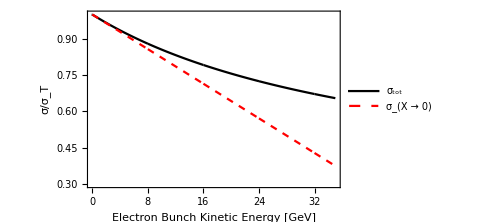

```mathematica
σLowEnergy=ListLinePlot[{Partition[Riffle[σtotEe⟦All,1⟧,σtotEe⟦All,2⟧],2],Partition[Riffle[σtotEe⟦All,1⟧,σtotEe⟦All,3⟧],2]},Frame->True,FrameLabel->{"Electron Bunch Kinetic Energy [GeV]","σ/σ_T"},PlotStyle->{Black,{Red,Dashed}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"σ_tot","σ_(X → 0)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.8,0.8}],PlotRange->{{5 MeV/GeV,35 GeV/GeV},{0.3,1}},ImageSize->Medium]
```

```mathematica
σtotEe2=Table[{Ee/GeV,σtot[Ee,0,1064nm]/σT,σc[Ee,0,1064nm]/σT,σXbig[Ee,0,1064nm]/σT},{Ee,35GeV,10TeV,1GeV}];
```

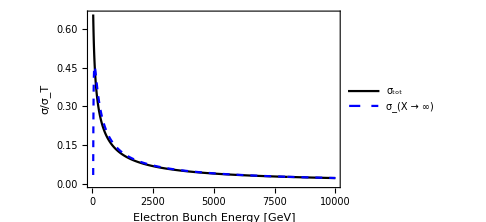

```mathematica
σHighEnergy=ListLinePlot[{Partition[Riffle[σtotEe2⟦All,1⟧,σtotEe2⟦All,2⟧],2],Partition[Riffle[σtotEe2⟦All,1⟧,σtotEe2⟦All,4⟧],2]},Frame->True,FrameLabel->{"Electron Bunch Energy [GeV]","σ/σ_T"},PlotStyle->{Black,{Blue,Dashed}},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"σ_tot","σ_(X → ∞)"},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.8,0.8}],PlotRange->Full,ImageSize->Medium]
```

```mathematica
σtotEe2⟦Position[σtotEe2⟦All,4⟧,Max[σtotEe2⟦All,4⟧]]⟦1,1⟧,1⟧
```

92

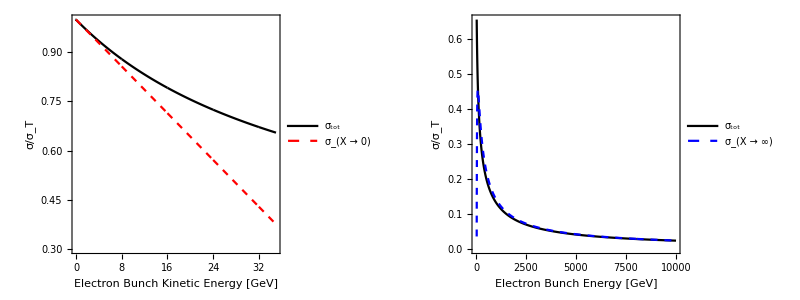

```mathematica
σEeplot=Grid[{{σLowEnergy,σHighEnergy}}]
```

### dσ/dE_γ Cross Section Spectral Density

```mathematica
dσdEγ[Ee_,λ_,ϕ_,θ_]:=(8*π*re^2)/(X[Ee,ϕ,λ]*(Ee-EL[λ]))*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

```mathematica
dσdEγCaseCplot=Table[{Eγ[Ee,0,λ,θ]/Eγ[Ee,0,λ,0]/.CaseA,dσdEγ[Ee,λ,0,θ]/dσdEγ[Ee,λ,0,0]/.CaseA},{θ,0,2*π,(2*π)/10^5}];
```

```mathematica
HighLim={{0,1},{1,1}};
```

```mathematica
LowLim={{0,0.5},{1,0.5}};
```

```mathematica
LowEdge={{0,0},{0,1}};
```

```mathematica
HighEdge={{1,1},{1,0}};
```

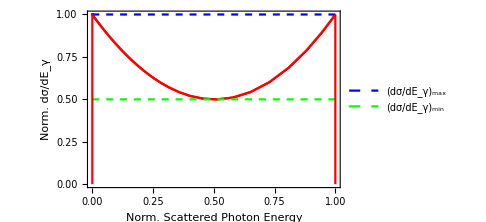

```mathematica
dσdEγplot=ListLinePlot[{dσdEγCaseCplot,HighLim,LowLim,LowEdge,HighEdge},Frame->True,FrameLabel->{"Norm. Scattered Photon Energy","Norm. dσ/dE_γ"},PlotStyle->{Red,{Dashed,Blue},{Dashed,Green},Red,Red},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{None,"(dσ/dE_γ)_max","(dσ/dE_γ)_min",None,None},LabelStyle->{12,FontFamily->"Times New Roman Baltic",FontColor->Black},LegendFunction->frame],{0.3,0.25}],PlotRange->Full,ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Thesis_Plots"];
Export["Cross_Section_Scattered_Photon_Energy.pdf",dσdEγplot];
```

## Collimated Flux: Curatolo vs Me

### Collimated Flux: Curatolo vs Me (R_ACHG)

```mathematica
ColFluxCompCaseA=Table[{ψ[Ee,θcol]/.CaseA,Fcol[Ee,0,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.CaseA,FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,θcol]/.CaseA},{θcol,0,1/γ[Ee]/.CaseA,1/(1000*γ[Ee])/.CaseA}];
```

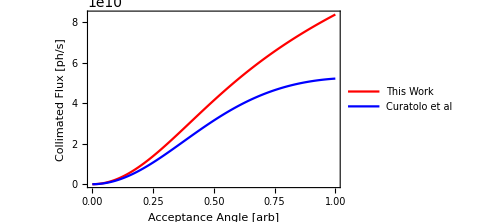

```mathematica
CaseACFcomp=ListLinePlot[{Partition[Riffle[ColFluxCompCaseA⟦All,1⟧,ColFluxCompCaseA⟦All,2⟧],2],Partition[Riffle[ColFluxCompCaseA⟦All,1⟧,ColFluxCompCaseA⟦All,3⟧],2]},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"This Work","Curatolo et al"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],ImageSize->Medium]
```

```mathematica
ColFluxCompCaseB=Table[{ψ[Ee,θcol]/.CaseB,Fcol[Ee,0,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.CaseB,FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,θcol]/.CaseB},{θcol,0,1/γ[Ee]/.CaseB,1/(1000*γ[Ee])/.CaseB}];
```

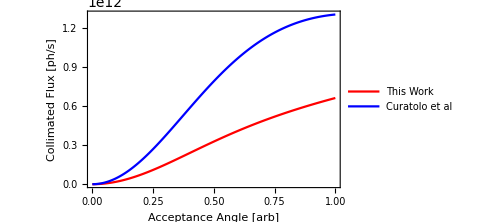

```mathematica
CaseBCFcomp=ListLinePlot[{Partition[Riffle[ColFluxCompCaseB⟦All,1⟧,ColFluxCompCaseB⟦All,2⟧],2],Partition[Riffle[ColFluxCompCaseB⟦All,1⟧,ColFluxCompCaseB⟦All,3⟧],2]},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"This Work","Curatolo et al"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],ImageSize->Medium]
```

```mathematica
Fcol[Ee,0,λ,0.5mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.CaseB
```

4.75295×10^11

```mathematica
FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,0.5mrad]/.CaseB
```

1.09402×10^12

```mathematica
RACHG[0,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.CaseB
```

0.274175

```mathematica
ColFluxCompCaseC=Table[{ψ[Ee,θcol]/.CaseC,Fcol[Ee,0,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.CaseC,FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,θcol]/.CaseC},{θcol,0,1/γ[Ee]/.CaseC,1/(1000*γ[Ee])/.CaseC}];
```

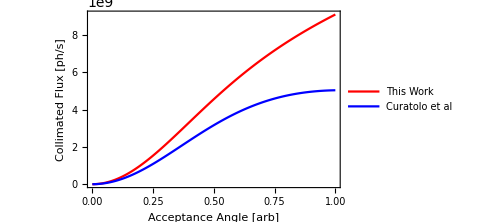

```mathematica
CaseCCFcomp=ListLinePlot[{Partition[Riffle[ColFluxCompCaseC⟦All,1⟧,ColFluxCompCaseC⟦All,2⟧],2],Partition[Riffle[ColFluxCompCaseC⟦All,1⟧,ColFluxCompCaseC⟦All,3⟧],2]},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"This Work","Curatolo et al"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],ImageSize->Medium]
```

```mathematica
CasesCFgrid=Grid[{{CaseACFcomp,CaseBCFcomp},{CaseCCFcomp}}]
```

-Graphics- | -Graphics-
-Graphics- |

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

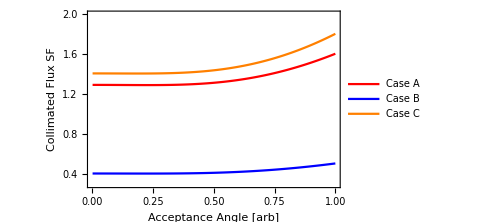

```mathematica
CasesSF=ListLinePlot[{Partition[Riffle[ColFluxCompCaseA⟦All,1⟧,ColFluxCompCaseA⟦All,2⟧/ColFluxCompCaseA⟦All,3⟧],2],Partition[Riffle[ColFluxCompCaseB⟦All,1⟧,ColFluxCompCaseB⟦All,2⟧/ColFluxCompCaseB⟦All,3⟧],2],Partition[Riffle[ColFluxCompCaseC⟦All,1⟧,ColFluxCompCaseC⟦All,2⟧/ColFluxCompCaseC⟦All,3⟧],2]},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux SF"},PlotStyle->{Red,Blue,Orange},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Case A","Case B","Case C"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.32}],PlotRange->{{0,1},{0.3,2}},ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Thesis_Plots"];
Export["Opt_Char_Fcol_Curatolo_Comp_CaseABC.pdf",CasesCFgrid];
Export["Opt_Char_Fcol_Curatolo_SF.pdf",CasesSF];
```

### Collimated Flux: Curatolo vs Me (R_ACHG Removed)

```mathematica
ColFluxCompCaseAnoRACHG=Table[{ψ[Ee,θcol]/.CaseA,Fcol[Ee,0,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/RACHG[0,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.CaseA,FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,θcol]/.CaseA},{θcol,0,1/γ[Ee]/.CaseA,1/(1000*γ[Ee])/.CaseA}];
```

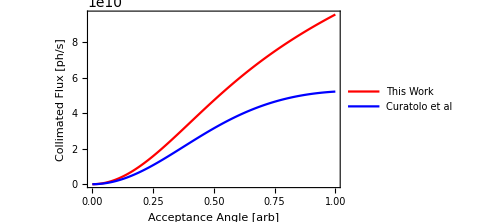

```mathematica
CaseACFcompnoRACHG=ListLinePlot[{Partition[Riffle[ColFluxCompCaseAnoRACHG⟦All,1⟧,ColFluxCompCaseAnoRACHG⟦All,2⟧],2],Partition[Riffle[ColFluxCompCaseA⟦All,1⟧,ColFluxCompCaseA⟦All,3⟧],2]},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"This Work","Curatolo et al"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],ImageSize->Medium]
```

```mathematica
ColFluxCompCaseBnoRACHG=Table[{ψ[Ee,θcol]/.CaseB,Fcol[Ee,0,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/RACHG[0,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.CaseB,FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,θcol]/.CaseB},{θcol,0,1/γ[Ee]/.CaseB,1/(1000*γ[Ee])/.CaseB}];
```

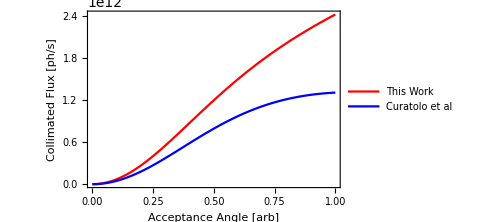

```mathematica
CaseBCFcompnoRACHG=ListLinePlot[{Partition[Riffle[ColFluxCompCaseBnoRACHG⟦All,1⟧,ColFluxCompCaseBnoRACHG⟦All,2⟧],2],Partition[Riffle[ColFluxCompCaseB⟦All,1⟧,ColFluxCompCaseB⟦All,3⟧],2]},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"This Work","Curatolo et al"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],ImageSize->Medium]
```

```mathematica
RACHG[0,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.CaseB
```

0.274175

```mathematica
ColFluxCompCaseCnoRACHG=Table[{ψ[Ee,θcol]/.CaseC,Fcol[Ee,0,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/RACHG[0,βIPx,βIPy,Ee,ϵnx,ϵny,σL,σze,tpulse,λ]/.CaseC,FcolCuratolo[Ee,0,λ,Q,Epulse,βIPx,βIPy,ϵnx,ϵny,σL,f,θcol]/.CaseC},{θcol,0,1/γ[Ee]/.CaseC,1/(1000*γ[Ee])/.CaseC}];
```

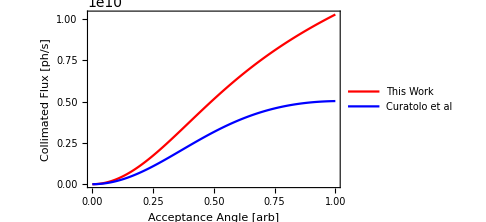

```mathematica
CaseCCFcompnoRACHG=ListLinePlot[{Partition[Riffle[ColFluxCompCaseCnoRACHG⟦All,1⟧,ColFluxCompCaseCnoRACHG⟦All,2⟧],2],Partition[Riffle[ColFluxCompCaseC⟦All,1⟧,ColFluxCompCaseC⟦All,3⟧],2]},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"This Work","Curatolo et al"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],ImageSize->Medium]
```

```mathematica
CasesCFgridnoRACHG=Grid[{{CaseACFcompnoRACHG,CaseBCFcompnoRACHG},{CaseCCFcompnoRACHG}}]
```

-Graphics- | -Graphics-
-Graphics- |

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

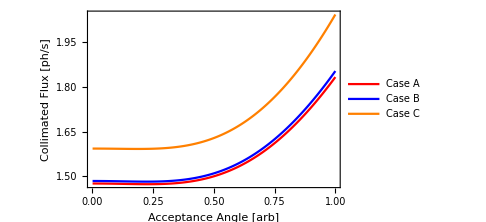

```mathematica
CasesSFnoRACHG=ListLinePlot[{Partition[Riffle[ColFluxCompCaseAnoRACHG⟦All,1⟧,ColFluxCompCaseAnoRACHG⟦All,2⟧/ColFluxCompCaseAnoRACHG⟦All,3⟧],2],Partition[Riffle[ColFluxCompCaseBnoRACHG⟦All,1⟧,ColFluxCompCaseBnoRACHG⟦All,2⟧/ColFluxCompCaseBnoRACHG⟦All,3⟧],2],Partition[Riffle[ColFluxCompCaseCnoRACHG⟦All,1⟧,ColFluxCompCaseCnoRACHG⟦All,2⟧/ColFluxCompCaseCnoRACHG⟦All,3⟧],2]},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{Red,Blue,Orange},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"Case A","Case B","Case C"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.72}],ImageSize->Medium]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Thesis_Plots"];
Export["Opt_Char_Fcol_Curatolo_Comp_CaseABC_noRACHG.pdf",CasesCFgridnoRACHG];
Export["Opt_Char_Fcol_Curatolo_SF_noRACHG.pdf",CasesSFnoRACHG];
```

### Final Comparison Plots

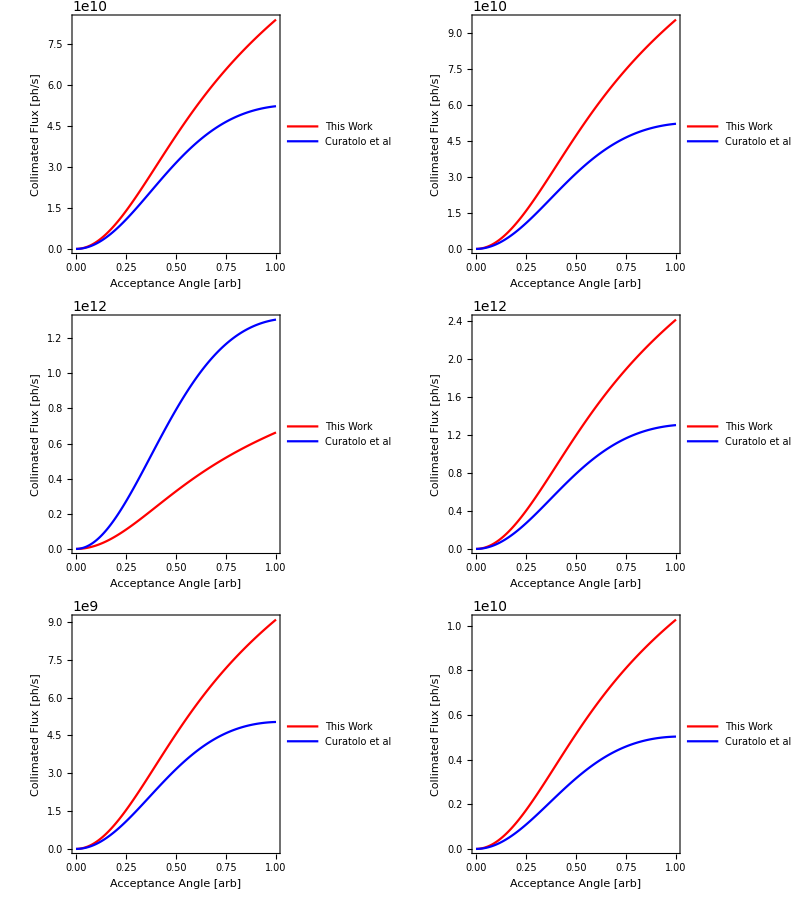

```mathematica
CuratoloCompGrid=Grid[{{CaseACFcomp,CaseACFcompnoRACHG},{CaseBCFcomp,CaseBCFcompnoRACHG},{CaseCCFcomp,CaseCCFcompnoRACHG}}]
```

```mathematica
CuratoloSFGrid=Grid[{{CasesSF,CasesSFnoRACHG}}]
```

CasesSF | -Graphics-

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Thesis_Plots"];
Export["Opt_Char_Fcol_Curatolo_Comp_FINAL.pdf",CuratoloCompGrid];
Export["Opt_Char_Fcol_Curatolo_SF_FINAL.pdf",CuratoloSFGrid];
```

## ICARUS Ψ Simulations

These are still a work in progress...

```mathematica
Ψval=Table[Ψ,{Ψ,0.1,0.9,0.1}];
```

### Case A

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/CaseA/CaseA_PSI"];
```

```mathematica
datasetCaseA[Ψval_]:=<<("CASE_A_PSI"<>ToString[Ψval]<>"_QMC_20M.txt");
```

```mathematica
ΨdataCaseA=Table[{Ψ,Integrate[Interpolation[datasetCaseA[Ψ]⟦2⟧][x],{x,Min[datasetCaseA[Ψ]⟦2,All,1⟧],Max[datasetCaseA[Ψ]⟦2,All,1⟧]}]*(Q*f)/nC/.CaseA},{Ψ,0.1,0.9,0.1}]
```

{{0.1,2.78612×10^9},{0.2,1.04063×10^10},{0.3,2.15749×10^10},{0.4,3.39991×10^10},{0.5,4.42351×10^10},{0.6,5.64135×10^10},{0.7,6.76414×10^10},{0.8,7.20312×10^10},{0.9,8.59329×10^10}}

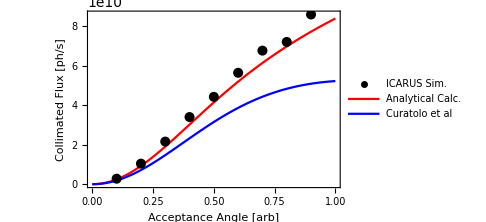

```mathematica
CaseACFcomp=ListPlot[{ΨdataCaseA,Partition[Riffle[ColFluxCompCaseA⟦All,1⟧,ColFluxCompCaseA⟦All,2⟧],2],Partition[Riffle[ColFluxCompCaseA⟦All,1⟧,ColFluxCompCaseA⟦All,3⟧],2]},Joined->{False,True,True},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{{Black,PointSize[0.02]},Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"ICARUS Sim.","Analytical Calc.","Curatolo et al"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.75}],ImageSize->Medium]
```

### Case B

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/Opt_Char_Thesis/CaseB/CaseB_PSI"];
```

```mathematica
datasetCaseB[Ψval_]:=<<("CASE_B_PSI"<>ToString[Ψval]<>"_QMC_20M.txt");
```

```mathematica
ΨdataCaseB=Table[{Ψ,Integrate[Interpolation[datasetCaseB[Ψ]⟦2⟧][x],{x,Min[datasetCaseB[Ψ]⟦2,All,1⟧],Max[datasetCaseB[Ψ]⟦2,All,1⟧]}]*(Q*f)/nC/.CaseB},{Ψ,0.1,0.9,0.1}]
```

{{0.1,6.64452×10^10},{0.2,3.93649×10^10},{0.3,8.18134×10^10},{0.4,1.29382×10^11},{0.5,1.76601×10^11},{0.6,2.22725×10^11},{0.7,2.6589×10^11},{0.8,2.96888×10^11},{0.9,3.27821×10^11}}

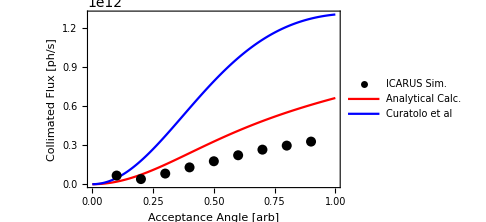

```mathematica
CaseBCFcomp=ListPlot[{ΨdataCaseB,Partition[Riffle[ColFluxCompCaseB⟦All,1⟧,ColFluxCompCaseB⟦All,2⟧],2],Partition[Riffle[ColFluxCompCaseB⟦All,1⟧,ColFluxCompCaseB⟦All,3⟧],2]},Joined->{False,True,True},Frame->True,FrameLabel->{"Acceptance Angle [arb]","Collimated Flux [ph/s]"},PlotStyle->{{Black,PointSize[0.02]},Red,Blue},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotLegends->Placed[LineLegend[{"ICARUS Sim.","Analytical Calc.","Curatolo et al"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.25,0.75}],ImageSize->Medium]
```

## FEBE ICS Updated

```mathematica
d=10;
```

```mathematica
a[d_,θ_]:=d*Tan[θ];
```

### Case A

```mathematica
F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEA//ScientificForm
```

2.9173×10^7

```mathematica
Fcol[Ee,ϕ,λ,9.8μrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEA
```

1010.12

```mathematica
a[d,9.8μrad]/mm
```

0.098

```mathematica
Fcol[Ee,ϕ,λ,0.031mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,10pC,Epulse,f]/.FEBE250CASEA
```

1010.33

```mathematica
a[d,0.031mrad]/mm
```

0.31

### Case B

```mathematica
F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEB//ScientificForm
```

5.83436×10^5

```mathematica
Fcol[Ee,ϕ,λ,0.07mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEB
```

1028.32

```mathematica
a[d,0.07mrad]/mm
```

0.7

```mathematica
Fcol[Ee,ϕ,λ,0.221mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,10pC,Epulse,f]/.FEBE250CASEB
```

1003.83

```mathematica
a[d,0.221mrad]/mm
```

2.21

```mathematica
θcolCASEB=Table[{θcol/mrad,Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEB,Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,10pC,Epulse,f]/.FEBE250CASEB,100*rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.FEBE250CASEB,((Eγ[Ee,ϕ,λ,0mrad]/.FEBE250CASEB)*(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.FEBE250CASEB)*2*Sqrt[2*Log[2]]*3)/MeV},{θcol,0,1mrad,0.01mrad}];
```

```mathematica
FcolθcolQ100CASEB=ListLinePlot[Partition[Riffle[θcolCASEB⟦All,1⟧,θcolCASEB⟦All,2⟧],2],PlotStyle->{Blue},Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/bunch]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,1},{0,1.5*10^5}},ImageSize->Medium];
```

```mathematica
FcolθcolQ10CASEB=ListLinePlot[Partition[Riffle[θcolCASEB⟦All,1⟧,θcolCASEB⟦All,3⟧],2],PlotStyle->{Blue},Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/bunch]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,1},{0,1.5*10^4}},ImageSize->Medium];
```

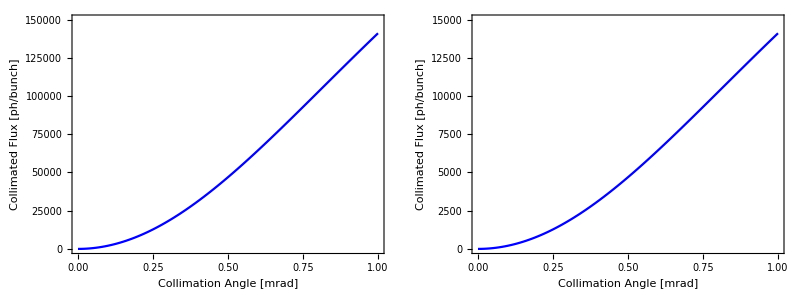

```mathematica
CASEBFcolθcol=Grid[{{FcolθcolQ100CASEB,FcolθcolQ10CASEB}}]
```

```mathematica
rmsBWθcolCASEB=ListLinePlot[Partition[Riffle[θcolCASEB⟦All,1⟧,θcolCASEB⟦All,4⟧],2],PlotStyle->{Red},Frame->True,FrameLabel->{"Collimation Angle [mrad]","rms Bandwidth [%]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,1},{3,7}},ImageSize->Medium];
```

```mathematica
ΔEγθcolCASEB=ListLinePlot[Partition[Riffle[θcolCASEB⟦All,1⟧,θcolCASEB⟦All,5⟧],2],PlotStyle->{Orange},Frame->True,FrameLabel->{"Collimation Angle [mrad]","Spectral Range [MeV]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,1},{0.3,0.8}},ImageSize->Medium];
```

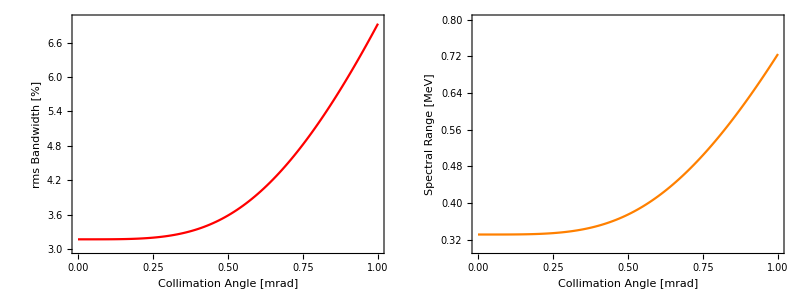

```mathematica
CASEBrmsBWSpecRangeθcol=Grid[{{rmsBWθcolCASEB,ΔEγθcolCASEB}}]
```

```mathematica
FcolrmsBWQ100CASEB=ListLinePlot[Partition[Riffle[θcolCASEB⟦All,4⟧,θcolCASEB⟦All,2⟧],2],PlotStyle->{Green},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/bunch]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{3,7},{0,1.5*10^5}},ImageSize->Medium];
```

```mathematica
FcolrmsBWQ10CASEB=ListLinePlot[Partition[Riffle[θcolCASEB⟦All,4⟧,θcolCASEB⟦All,3⟧],2],PlotStyle->{Green},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/bunch]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{3,7},{0,1.5*10^4}},ImageSize->Medium];
```

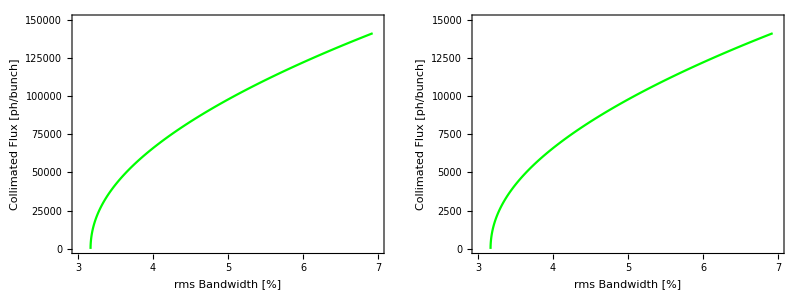

```mathematica
CASEBFcolrmsBW=Grid[{{FcolrmsBWQ100CASEB,FcolrmsBWQ10CASEB}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FEBE_PLOTS/CASE_B_LASER"];
Export["FEBE250_CASEB_Fcolvsthetacol.pdf",CASEBFcolθcol];
Export["FEBE250_CASEB_rmsBW_SpectralRangevsthetacol.pdf",CASEBrmsBWSpecRangeθcol];
Export["FEBE250_CASEB_FcolvsrmsBW.pdf",CASEBFcolrmsBW];
```

### Case C

```mathematica
F[Ee,ϕ,λ,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEC//ScientificForm
```

4.62669×10^5

```mathematica
Fcol[Ee,ϕ,λ,0.078mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEC
```

1013.4

```mathematica
a[d,0.078mrad]/mm
```

0.78

```mathematica
Fcol[Ee,ϕ,λ,0.249mrad,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,10pC,Epulse,f]/.FEBE250CASEC
```

1005.75

```mathematica
a[d,0.249mrad]/mm
```

2.49

```mathematica
θcolCASEC=Table[{θcol/mrad,Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,Q,Epulse,f]/.FEBE250CASEC,Fcol[Ee,ϕ,λ,θcol,βIPx,βIPy,ϵnx,ϵny,σL,σze,tpulse,10pC,Epulse,f]/.FEBE250CASEC,100*rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.FEBE250CASEC,((Eγ[Ee,ϕ,λ,0mrad]/.FEBE250CASEC)*(rmsBandwidth[Ee,λ,θcol,ϕ,ΔEe,Δλ,ϵnx,ϵny,βIPx,βIPy]/.FEBE250CASEC)*2*Sqrt[2*Log[2]]*3)/MeV},{θcol,0,1mrad,0.01mrad}];
```

```mathematica
FcolθcolQ100CASEC=ListLinePlot[Partition[Riffle[θcolCASEC⟦All,1⟧,θcolCASEC⟦All,2⟧],2],PlotStyle->{Blue},Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/bunch]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,1},{0,1.2*10^5}},ImageSize->Medium];
```

```mathematica
FcolθcolQ10CASEC=ListLinePlot[Partition[Riffle[θcolCASEC⟦All,1⟧,θcolCASEC⟦All,3⟧],2],PlotStyle->{Blue},Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/bunch]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,1},{0,1.2*10^4}},ImageSize->Medium];
```

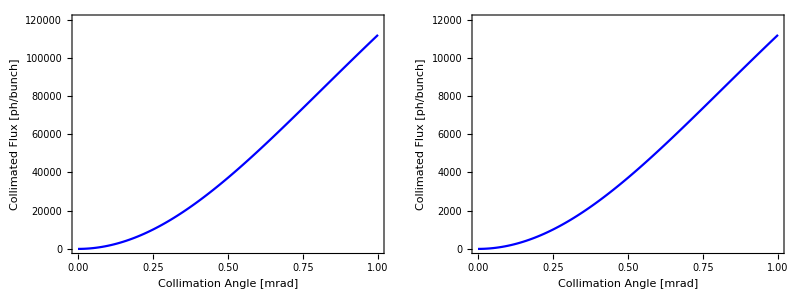

```mathematica
CASECFcolθcol=Grid[{{FcolθcolQ100CASEC,FcolθcolQ10CASEC}}]
```

```mathematica
rmsBWθcolCASEC=ListLinePlot[Partition[Riffle[θcolCASEC⟦All,1⟧,θcolCASEC⟦All,4⟧],2],PlotStyle->{Red},Frame->True,FrameLabel->{"Collimation Angle [mrad]","rms Bandwidth [%]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,1},{0,6.5}},ImageSize->Medium];
```

```mathematica
ΔEγθcolCASEC=ListLinePlot[Partition[Riffle[θcolCASEC⟦All,1⟧,θcolCASEC⟦All,5⟧],2],PlotStyle->{Orange},Frame->True,FrameLabel->{"Collimation Angle [mrad]","Spectral Range [MeV]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,1},{0,0.5}},ImageSize->Medium];
```

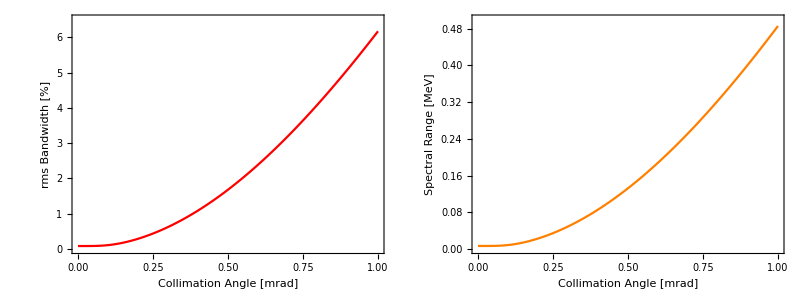

```mathematica
CASECrmsBWSpecRangeθcol=Grid[{{rmsBWθcolCASEC,ΔEγθcolCASEC}}]
```

```mathematica
FcolrmsBWQ100CASEC=ListLinePlot[Partition[Riffle[θcolCASEC⟦All,4⟧,θcolCASEC⟦All,2⟧],2],PlotStyle->{Green},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/bunch]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,6},{0,1.2*10^5}},ImageSize->Medium];
```

```mathematica
FcolrmsBWQ10CASEC=ListLinePlot[Partition[Riffle[θcolCASEC⟦All,4⟧,θcolCASEC⟦All,3⟧],2],PlotStyle->{Green},Frame->True,FrameLabel->{"rms Bandwidth [%]","Collimated Flux [ph/bunch]"},LabelStyle->{15,FontFamily->"Times New Roman Baltic",FontColor->Black},PlotRange->{{0,6},{0,1.2*10^4}},ImageSize->Medium];
```

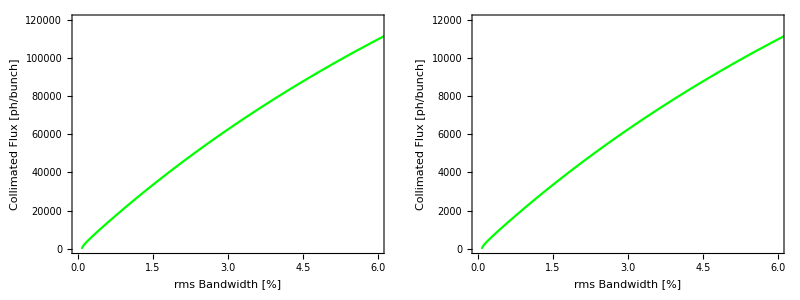

```mathematica
CASECFcolrmsBW=Grid[{{FcolrmsBWQ100CASEC,FcolrmsBWQ10CASEC}}]
```

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/FEBE_PLOTS/CASE_C_LASER"];
Export["FEBE250_CASEC_Fcolvsthetacol.pdf",CASECFcolθcol];
Export["FEBE250_CASEC_rmsBW_SpectralRangevsthetacol.pdf",CASECrmsBWSpecRangeθcol];
Export["FEBE250_CASEC_FcolvsrmsBW.pdf",CASECFcolrmsBW];
```

## Optimisation: Collimation Angle variation with energy (CBETA, Thomson Regime)

Energy adjusted look at the CBETA ICS source optimisationas for the round beam case to see the underlying collimation angle behaviour.

```mathematica
Eevals={42,78,114,150}*MeV;
```

```mathematica
γvals=(Eevals+me)/me
```

{83.1919,153.642,224.092,294.543}

```mathematica
θcolvals={1.533,0.830,0.569,0.433}*mrad
```

{0.001533,0.00083,0.000569,0.000433}

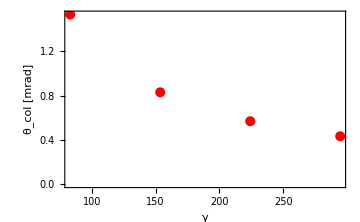

```mathematica
ListPlot[Partition[Riffle[γvals,θcolvals/mrad],2],Frame->True,FrameLabel->{"γ","θ_col [mrad]"},PlotStyle->{Red,PointSize[0.02]},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium]
```

```mathematica
γvals*θcolvals
```

{0.127533,0.127523,0.127509,0.127537}

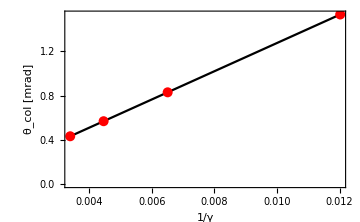

```mathematica
ListPlot[{Partition[Riffle[1/γvals,θcolvals/mrad],2],Partition[Riffle[1/γvals,θcolvals/mrad],2]},Joined->{False,True},Frame->True,FrameLabel->{"1/γ","θ_col [mrad]"},PlotStyle->{{Red,PointSize[0.02]},Black},LabelStyle->{16,FontFamily->"Times New Roman Baltic",FontColor->Black},ImageSize->Medium]
```

```mathematica
recipΔγ=1/(γvals/γvals⟦1⟧)
```

{1.,0.541466,0.371239,0.282444}

```mathematica
Δθcol=θcolvals/θcolvals⟦1⟧
```

{1.,0.541422,0.371168,0.282453}